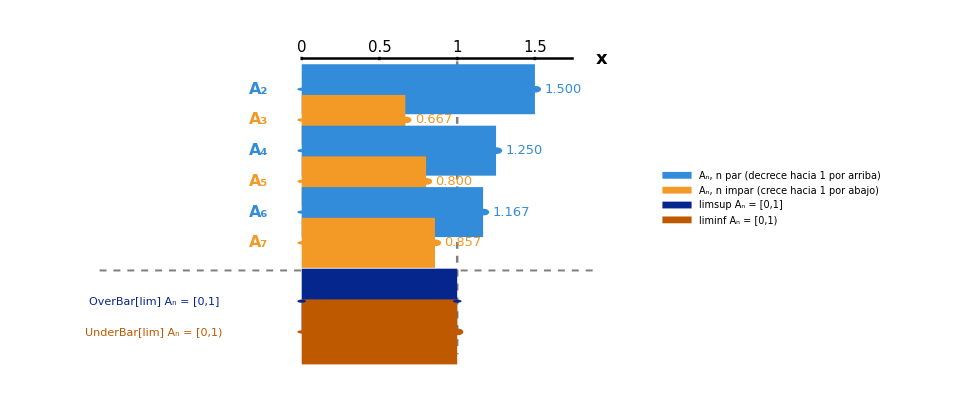
Aₙ = [0, 1+(-1)ⁿ/n)

-Graphics-

```mathematica
nMin=2;nMax=7;
sep=0.55;
rDot=0.028;

xn[n_]:=1+(-1)^n/n;

colorPar=RGBColor[0.2,0.55,0.85];    (*n par:decrece hacia 1 por arriba*)
colorImpar=RGBColor[0.95,0.6,0.15];  (*n impar:crece hacia 1 por abajo*)
colorLimsup=RGBColor[0.02,0.15,0.55];
colorLiminf=RGBColor[0.75,0.35,0.0];

subInd[n_Integer]:=StringJoin[Characters[ToString[n]]/. {"0"->"₀","1"->"₁","2"->"₂","3"->"₃","4"->"₄","5"->"₅","6"->"₆","7"->"₇","8"->"₈","9"->"₉"}];

closedDot[center_,col_]:={col,Disk[center,rDot]};
openDot[center_,col_]:={White,Disk[center,rDot],col,Thickness[0.0035],Circle[center,rDot]};

(*----------filas de A_n,n=2,...,7----------*)
filas=Table[Module[{y,x,col},y=-(n-nMin) sep;
x=xn[n];
col=If[EvenQ[n],colorPar,colorImpar];
{col,Thickness[0.05],CapForm["Round"],Line[{{0,y},{x,y}}],closedDot[{0,y},col],openDot[{x,y},col],Text[Style["A"<>subInd[n],16,Bold],{-0.28,y}],Text[Style[ToString[NumberForm[N[x],{4,3}]],13],{x+0.18,y}]}],{n,nMin,nMax}];

(*----------filas resumen:liminf y limsup----------*)
yUltimaFila=-(nMax-nMin) sep;
ySepLinea=yUltimaFila-0.9 sep;
yLimsup=ySepLinea-sep;
yLiminf=yLimsup-sep;

filaLimsup={colorLimsup,Thickness[0.065],CapForm["Round"],Line[{{0,yLimsup},{1,yLimsup}}],closedDot[{0,yLimsup},colorLimsup],closedDot[{1,yLimsup},colorLimsup],Text[Row[{OverBar[Style["lim",16,Bold]],Style[" Aₙ = [0,1]",16,Bold]}],{-0.95,yLimsup}]};

filaLiminf={colorLiminf,Thickness[0.065],CapForm["Round"],Line[{{0,yLiminf},{1,yLiminf}}],closedDot[{0,yLiminf},colorLiminf],openDot[{1,yLiminf},colorLiminf],Text[Row[{UnderBar[Style["lim",16,Bold]],Style[" Aₙ = [0,1)",16,Bold]}],{-0.95,yLiminf}]};

lineaSeparadora={Gray,Dashed,Thickness[0.002],Line[{{-1.3,ySepLinea},{1.9,ySepLinea}}]};

(*----------eje real----------*)
xMaxPlot=1.75;
ejeReal={Black,Thickness[0.0025],Line[{{0,0.55},{xMaxPlot,0.55}}],Table[Line[{{k,0.52},{k,0.58}}],{k,0,1.5,0.5}],Text[Style["0",15],{0,0.75}],Text[Style["0.5",15],{0.5,0.75}],Text[Style["1",15],{1,0.75}],Text[Style["1.5",15],{1.5,0.75}],Text[Style["x",18,Bold],{xMaxPlot+0.18,0.55}]};

lineaUno={Gray,Dashed,Thickness[0.0025],Line[{{1,0.5},{1,yLiminf-0.4}}]};

grafico=Graphics[{lineaUno,ejeReal,filas,lineaSeparadora,filaLimsup,filaLiminf},PlotRange->{{-1.4,xMaxPlot+0.4},{yLiminf-0.5,0.95}},AspectRatio->0.55,ImageSize->720];

imagenFinal=Legended[grafico,SwatchLegend[{colorPar,colorImpar,colorLimsup,colorLiminf},{"Aₙ, n par (decrece hacia 1 por arriba)","Aₙ, n impar (crece hacia 1 por abajo)","limsup Aₙ = [0,1]","liminf Aₙ = [0,1)"},LabelStyle->Directive[FontSize->15],LegendMarkerSize->20]];

imagenCompleta=Column[{Style["Aₙ = [0, 1+(-1)ⁿ/n)",18,Bold],Spacer[10],imagenFinal},Alignment->Center];

imagenCompleta
```

```mathematica
Export["Parcial1_P1.png",imagenCompleta,Background->White,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["Parcial1_P1.png"]]]
```

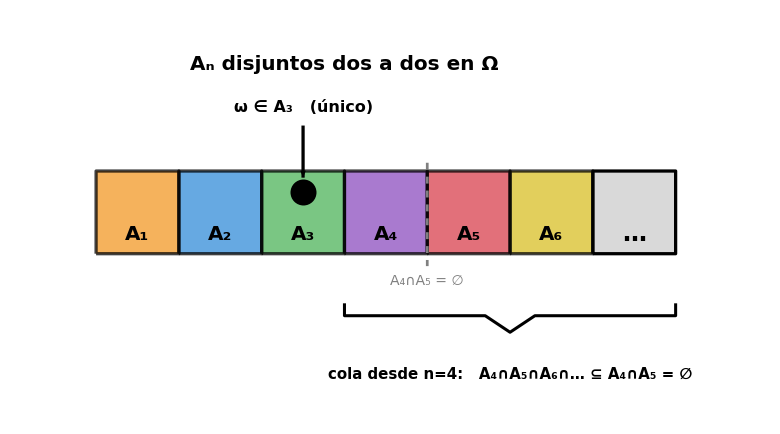
-Graphics-

UnderBar[lim] Aₙ = ∅   (toda cola se anula: cada Aₙ solo se solapa consigo mismo)
OverBar[lim] Aₙ = ∅   (ningún ω puede repetirse en dos bloques distintos)
⇒  lim Aₙ = ∅   (la sucesión converge)

```mathematica
nBloques=6;

coloresBloques={RGBColor[0.95,0.6,0.15],RGBColor[0.2,0.55,0.85],RGBColor[0.3,0.7,0.35],RGBColor[0.55,0.3,0.75],RGBColor[0.85,0.25,0.3],RGBColor[0.85,0.75,0.15]};

subInd[n_Integer]:=StringJoin[Characters[ToString[n]]/. {"0"->"₀","1"->"₁","2"->"₂","3"->"₃","4"->"₄","5"->"₅","6"->"₆","7"->"₇","8"->"₈","9"->"₉"}];

bloques=Table[{coloresBloques[[k]],Opacity[0.75],EdgeForm[{Black,Thickness[0.003]}],Rectangle[{k-1,0},{k,1},RoundingRadius->0.08],Black,Opacity[1],Text[Style["A"<>subInd[k],20,Bold],{k-0.5,0.25}]},{k,1,nBloques}];

bloqueElipsis={LightGray,EdgeForm[{Black,Thickness[0.003]}],Rectangle[{nBloques,0},{nBloques+1,1},RoundingRadius->0.08],Black,Text[Style["…",24,Bold],{nBloques+0.5,0.25}]};

(*Punto ω,perteneciente únicamente al bloque A3*)
nOmega=3;
xOmega=nOmega-0.5;

puntoOmega={Black,PointSize[0.024],Point[{xOmega,0.75}]};

flechaOmega={Black,Thickness[0.003],Arrowheads[0.025],Arrow[{{xOmega,1.55},{xOmega,0.92}}],Text[Style["ω ∈ A"<>subInd[nOmega]<>"   (único)",16,Bold],{xOmega,1.78}]};

(*Anotación:dos bloques adyacentes concretos,disjuntos,usados en la cola*)
nCola=4;
anotDisjunto={Gray,Dashed,Thickness[0.0025],Line[{{nCola,1.1},{nCola,-0.15}}],Text[Style["A"<>subInd[nCola]<>"∩A"<>subInd[nCola+1]<>" = ∅",14,Italic,Gray],{nCola,-0.32}]};

(*"Llave" bajo la cola a partir de n=4,para argumentar liminf=∅*)
xIzq=nCola-1;xDer=nBloques+1;
yBrace=-0.6;
brace={Black,Thickness[0.0028],Line[{{xIzq,yBrace},{xIzq,yBrace-0.15},{(xIzq+xDer)/2-0.3,yBrace-0.15},{(xIzq+xDer)/2,yBrace-0.35},{(xIzq+xDer)/2+0.3,yBrace-0.15},{xDer,yBrace-0.15},{xDer,yBrace}}]};

etiquetaBrace=Text[Style["cola desde n="<>ToString[nCola]<>":   A"<>subInd[nCola]<>"∩A"<>subInd[nCola+1]<>"∩A"<>subInd[nCola+2]<>"∩… ⊆ A"<>subInd[nCola]<>"∩A"<>subInd[nCola+1]<>" = ∅",15,Bold],{(xIzq+xDer)/2,yBrace-0.85}];

tituloPrincipal=Text[Style["Aₙ disjuntos dos a dos en Ω",20,Bold],{3,2.3}];

grafico=Graphics[{bloques,bloqueElipsis,anotDisjunto,puntoOmega,flechaOmega,brace,etiquetaBrace,tituloPrincipal},PlotRange->{{-0.3,nBloques+1.4},{yBrace-1.1,2.6}},ImageSize->780];

(*Conclusión,con la notación correcta liminf=UnderBar[lim],limsup=OverBar[lim]*)
conclusion=Column[{Row[{UnderBar[Style["lim",18,Bold]],Style[" Aₙ = ∅   (toda cola se anula: cada Aₙ solo se solapa consigo mismo)",17]}],Row[{OverBar[Style["lim",18,Bold]],Style[" Aₙ = ∅   (ningún ω puede repetirse en dos bloques distintos)",17]}],Style["⇒  lim Aₙ = ∅   (la sucesión converge)",18,Bold,Darker[Red]]},Alignment->Center,Spacings->0.9];

imagenFinal=Column[{grafico,Spacer[15],conclusion},Alignment->Center];

imagenFinal
```

```mathematica
Export["parcial1_P2.png",imagenFinal,Background->None,ImageResolution->300];
```

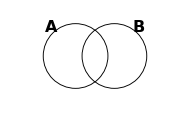
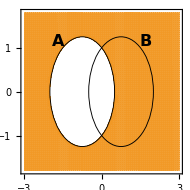
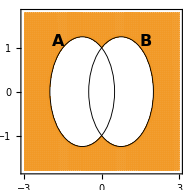
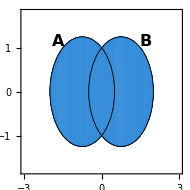
-Graphics-
A, B-Graphics--Graphics-
Aᶜ-Graphics--Graphics-
Aᶜ\B-Graphics--Graphics-
A∪B

```mathematica
sep=0.75;r=1.25;
limX=3.0;limY=1.8;

colorPaso=RGBColor[0.95,0.6,0.15];
colorFinal=RGBColor[0.2,0.55,0.85];

vennPanel[condicion_,color_,etiqueta_]:=Module[{capas,dibujo},capas=If[condicion===None,{},{RegionPlot[condicion,{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[color,Opacity[0.75]],BoundaryStyle->None,PlotPoints->80,MaxRecursion->3]}];
dibujo=Show[Sequence@@capas,Graphics[{Black,Thickness[0.0035],Circle[{-sep,0},r],Circle[{sep,0},r],Text[Style["A",16,Bold],{-sep-r+0.3,r-0.1}],Text[Style["B",16,Bold],{sep+r-0.3,r-0.1}]}],PlotRange->{{-limX,limX},{-limY,limY}},AspectRatio->Automatic,ImageSize->190];
Column[{dibujo,Style[etiqueta,17,Bold]},Alignment->Center,Spacings->0.4]];

flecha=Graphics[{Black,Thickness[0.006],Arrowheads[0.15],Arrow[{{0,0},{1,0}}]},ImageSize->{40,30},PlotRange->{{-0.1,1.1},{-0.3,0.3}}];

panel0=vennPanel[None,None,"A, B"];
panel1=vennPanel[!((x+sep)^2+y^2<r^2),colorPaso,"Aᶜ"];
panel2=vennPanel[!((x+sep)^2+y^2<r^2)&&!((x-sep)^2+y^2<r^2),colorPaso,"Aᶜ\\B"];
panel3=vennPanel[(x+sep)^2+y^2<r^2||(x-sep)^2+y^2<r^2,colorFinal,"A∪B"];

imagenFinal=Row[{panel0,flecha,panel1,flecha,panel2,flecha,panel3}];

imagenFinal
```

```mathematica
Export["parcial1_P3.png",imagenFinal,Background->White,ImageResolution->300];
```

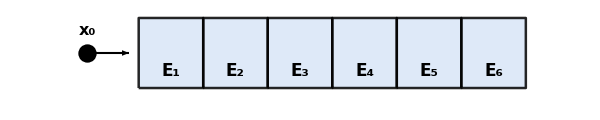
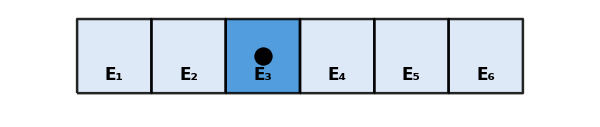
Caso a):  x₀ fuera de todos los Eₙ
-Graphics-

Caso b):  x₀ dentro de un único Eₙ₀
-Graphics-

```mathematica
nBloques=6;
nCasoB=3; (*bloque donde cae x0 en el caso b)*)

subInd[n_Integer]:=StringJoin[Characters[ToString[n]]/. {"0"->"₀","1"->"₁","2"->"₂","3"->"₃","4"->"₄","5"->"₅","6"->"₆","7"->"₇","8"->"₈","9"->"₉"}];

colorBase=RGBColor[0.85,0.9,0.97];
colorHit=RGBColor[0.2,0.55,0.85];

bloquesFila[nResaltado_]:=Table[{If[k==nResaltado,colorHit,colorBase],Opacity[0.85],EdgeForm[{Black,Thickness[0.003]}],Rectangle[{k-1,0},{k,1},RoundingRadius->0.08],Black,Opacity[1],Text[Style["E"<>subInd[k],17,Bold],{k-0.5,0.25}]},{k,1,nBloques}];

(*----------Panel a):x0 fuera de todos los bloques----------*)
panelA=Graphics[{bloquesFila[0],Black,PointSize[0.022],Point[{-0.8,0.5}],Thickness[0.0025],Arrowheads[0.02],Arrow[{{-0.8,0.5},{-0.15,0.5}}],Text[Style["x₀",16,Bold],{-0.8,0.82}]},PlotRange->{{-1.3,nBloques+0.3},{-0.3,1.1}},ImageSize->600];

tituloA=Style["Caso a):  x₀ fuera de todos los Eₙ",17,Bold];

(*----------Panel b):x0 dentro de un único bloque----------*)
xPuntoB=nCasoB-0.5;

panelB=Graphics[{bloquesFila[nCasoB],Black,PointSize[0.022],Point[{xPuntoB,0.5}]},PlotRange->{{-0.3,nBloques+0.3},{-0.3,1.1}},ImageSize->600];

tituloB=Style["Caso b):  x₀ dentro de un único Eₙ₀",17,Bold];

(*----------Composición final----------*)
imagenFinal=Column[{tituloA,panelA,Spacer[20],tituloB,panelB},Alignment->Center,Spacings->0.7];

imagenFinal
```

```mathematica
Export["parcial1_P4.png",imagenFinal,Background->White,ImageResolution->300];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["parcial1_P4.png"]]]
```